# Allele Surfing Scenario 1:

## Testing:

Read in parameters:

```mathematica
pars=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/pars1.csv"];
gmax=pars[[2,2]];
nPop=pars[[3,2]];
nOther=pars[[4,2]];
KK=pars[[5,2]];
```

Population size dynamics:

```mathematica
data=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data1.csv"][[;;,1;;-2]];
```

```mathematica
data2=Flatten[Table[{r,c,data[[r,c]]},{r,1,gmax},{c,1,nPop}],1];
```

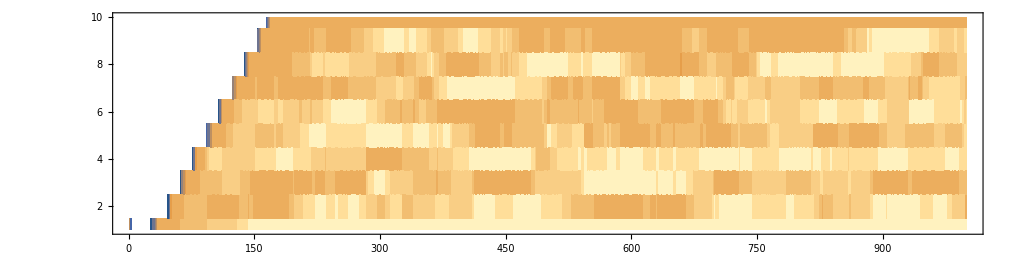

```mathematica
ListDensityPlot[data2,InterpolationOrder->0,AspectRatio->0.25]
```

Coalescent times:

## A single pair sample

```mathematica
coal=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data/coal1_0.csv"];
```

The number of possible lineages is given by the number of columns of coal

```mathematica
nLinF=Dimensions[coal][[2]]
```

20001

Draw a pair of lineages

```mathematica
sample=RandomSample[Range[nLinF],2]
```

{10019,14532}

The coalescent history of the sampled lineages is given by coalSample.  Each row is an individual, each column is a generation.

```mathematica
coalSample=Transpose[coal[[;;,sample]]];
```

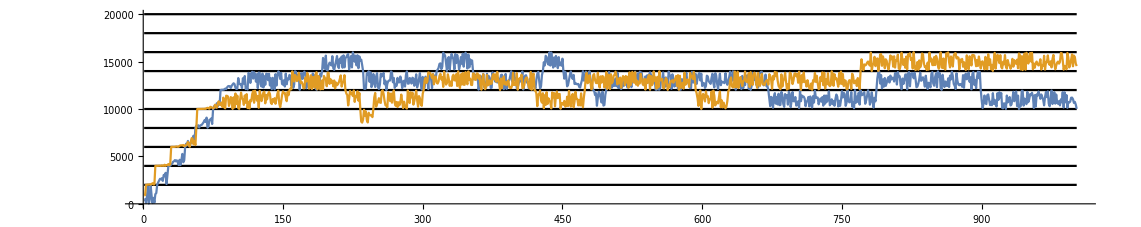

```mathematica
Show[Plot[Table[2KK p,{p,1,nPop}],{x,1,gmax+2},PlotStyle->Black],ListLinePlot[Transpose[coal[[;;,sample]]]],AspectRatio->0.2]
```

Calculating the coalescent times for a single sample

```mathematica
Tlist[sample_]:=Block[{g,ct,tlist},tlist={{1,0},{2,0}};
coalSample=Transpose[coal[[;;,sample]]];
For[g=1,g≤gmax+2,g++,
ct=CountDistinct[coalSample[[;;,g]]];
tlist[[ct,2]]++;
];
tlist
]
```

```mathematica
Tlist[sample]
```

{{1,0},{2,1002}}

Calculating coalescent times for different samples and keeping track of which demes they came from:

```mathematica
Clear[sample];
TLIST[n_]:=Block[{i,j,g,popi,popj,sample,mtrx,NoCo,ctmtrx},mtrx=Table[0,{i,1,nPop},{j,1,nPop}];ctmtrx=Table[0,{i,1,nPop},{j,1,nPop}];NoCo=0;
For[s=1,s≤n,s++,g=0;
(*Choosing a random sample*)
sample=RandomSample[Range[nLinF],2];
popi=Quotient[sample[[1]],2 KK]+1;
popj=Quotient[sample[[2]],2 KK]+1;
coalSample=Transpose[coal[[;;,sample]]];
If[CountDistinct[coalSample[[;;,g]]]==1,(*If coalescene occured*)
ctmtrx[[popi,popj]]++;
While[CountDistinct[coalSample[[;;,gmax+2-g]]]==2,mtrx[[popi,popj]]++;g++;],(*If no coalescence*)NoCo++]
];
Table[If[ctmtrx[[i,j]]>0,mtrx[[i,j]]/ctmtrx[[i,j]],0],{i,1,nPop},{j,1,nPop}]
]
```

```mathematica
Tout=TLIST[1500];
```

The i,j element is the average sampled coalescent time for lineages sampled in population i and population j.

```mathematica
MatrixForm[Tout]//N
```

(946.875 | 881.667 | 896.95 | 950.214 | 993.375 | 999.8 | 986.125 | 998.067 | 1002. | 999.25
937.706 | 940.462 | 1002. | 1002. | 999.688 | 998.333 | 1002. | 999.25 | 995.125 | 994.882
953.467 | 1002. | 925.833 | 869.833 | 931.231 | 1002. | 1002. | 1002. | 1002. | 981.55
1002. | 943.583 | 916.118 | 967.786 | 955.167 | 948.111 | 996.176 | 990.867 | 1002. | 953.882
1000.9 | 998.765 | 994.4 | 994.333 | 974.286 | 931.563 | 952.9 | 1002. | 985.176 | 995.231
997.611 | 993.583 | 998.071 | 994.875 | 992.438 | 946.692 | 988.6 | 986.8 | 991.333 | 985.083
991.842 | 991. | 992.222 | 996.909 | 994.923 | 988.067 | 877.583 | 995.077 | 986.563 | 998.
1000.31 | 1000.17 | 971.75 | 977.063 | 991.875 | 990.786 | 999.105 | 929.733 | 919.455 | 983.292
1000.71 | 995.538 | 1002. | 940.25 | 969.933 | 982.526 | 976.875 | 897.87 | 937.368 | 929.467
1000.31 | 1000.31 | 1002. | 950.75 | 957.875 | 988.313 | 998.706 | 956.929 | 901.077 | 872.)

The sampled within population coalescent time

```mathematica
Nwithin=N[Sum[Tout[[i,i]],{i,1,nPop}]/nPop]
```

931.862

The sampled between population coalescent time

```mathematica
Nall=N[Sum[Tout[[i,j]],{i,1,nPop},{j,1,nPop}]/nPop^2]
```

974.145

Coalescent Fst

```mathematica
(Nall-Nwithin)/Nwithin
```

0.0453752

Pairwise differences: